```mathematica
SetDirectory[NotebookDirectory[]];
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
rh=0.1;
rS=0.11;
rp={Sin[θp],
0,
Cos[θp]}*8*10^(-2);
p=10*{0,1,0}*10^(-9) ;
r={x,y,z};
q=Cross[p,rp];
R=r-rp;
f=Simplify[Sqrt[R.R](Sqrt[r.r]Sqrt[R.R]+r.R)];
Bp=Simplify[10^(5)Cross[p,R]/Sqrt[R.R]^3];
B=Simplify[10^(5)*(f q- Dot[q,r]D[f,{{x,y,z}}])/f^2];
```

```mathematica
norm[r_]:=Sqrt[r.r];
n=r/Sqrt[r.r];
er=n;
ez={0,0,1};
eϕ=Cross[ez,er];
eϕ=eϕ/norm@eϕ//Simplify;
eθ=Cross[eϕ,er]//Simplify;
nGeo={Cos@ϕG,0,Sin@ϕG};
```

## Fig1(c)

```mathematica
p1c=SliceVectorPlot3D[B/.{θp->0}/.Thread[{x,y,z}->{x1/100,y1/100,z1/100}],{x1^2+y1^2+z1^2==(rS*100)^2},{x1,-rS*100,rS*100},{y1,-rS*100,rS*100},{z1,0,rS*100},PlotLegends->Automatic,BoxRatios->{1, 1, 0.5},VectorPoints->15,VectorColorFunction->"Rainbow",AxesLabel->{"x (cm)","y (cm)","z (cm)"},VectorScaling->Automatic,VectorAspectRatio->0.25,VectorSizes->{0.5,1.5},ViewProjection->"Orthographic",ViewPoint->{0.5,0.5,0.5},ViewVertical->{0,0,1},Boxed->True,Axes->True,AxesEdge->{{1,-1},{1,-1},{1,-1}},AxesLabel->{None,None,None}]
```

-Graphics3D-

```mathematica
Export["subplots/fig1c.png",p1c];
```

## Fig1 (d)-(g)

```mathematica
ns={{x,y,z}/norm@{x,y,z},{1,0,0},{0,1,0},{0,0,1}};
fibPoints[n_]:=Module[{a},
a=(Sqrt@5+1)/2;
Table[Module[{ϕi,zi,θi},
ϕi=2Pi FractionalPart[i/a];
zi=1-(2i)/2/n;
θi=ArcCos@zi;
{Sin@θi Cos@ϕi,Sin@θi Sin@ϕi,zi}
]
,{i,0,n-1}]];
points=fibPoints[64];
vecs=Table[ns[[i]]/.Thread[{x,y,z}->#]&/@points,{i,4}];
p1d2g=Table[p1=Graphics3D[{{RGBColor[0.13,0.61,0.34],Arrowheads[0.03],Arrow[Tube[Transpose[{points,points+0.3vecs[[i]]}],0.01]]},(*Tube 控制箭头粗细*){colors[[1]],PointSize[0.015],Point[points]} (*可选：标记点位置*)
},BoxRatios->{1,1,{0.5,0.5,0.5,0.6}[[i]]},Axes->True,AxesLabel->{"x","y","z"}];
p2=SphericalPlot3D[1,{θ,0,Pi/2},{ϕ,0,2Pi},PlotStyle->Directive[Opacity[0.3],RGBColor[0.31,0.56,0.7]],MeshStyle->None];
Show[p1,p2,ViewProjection->"Orthographic",ViewPoint->{0.5,0.5,0.25},ViewVertical->{0,0,1},Boxed->False,Axes->False],{i,4}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Export["subplots/fig1d2g.png",p1d2g];
```

## Fig1(h)

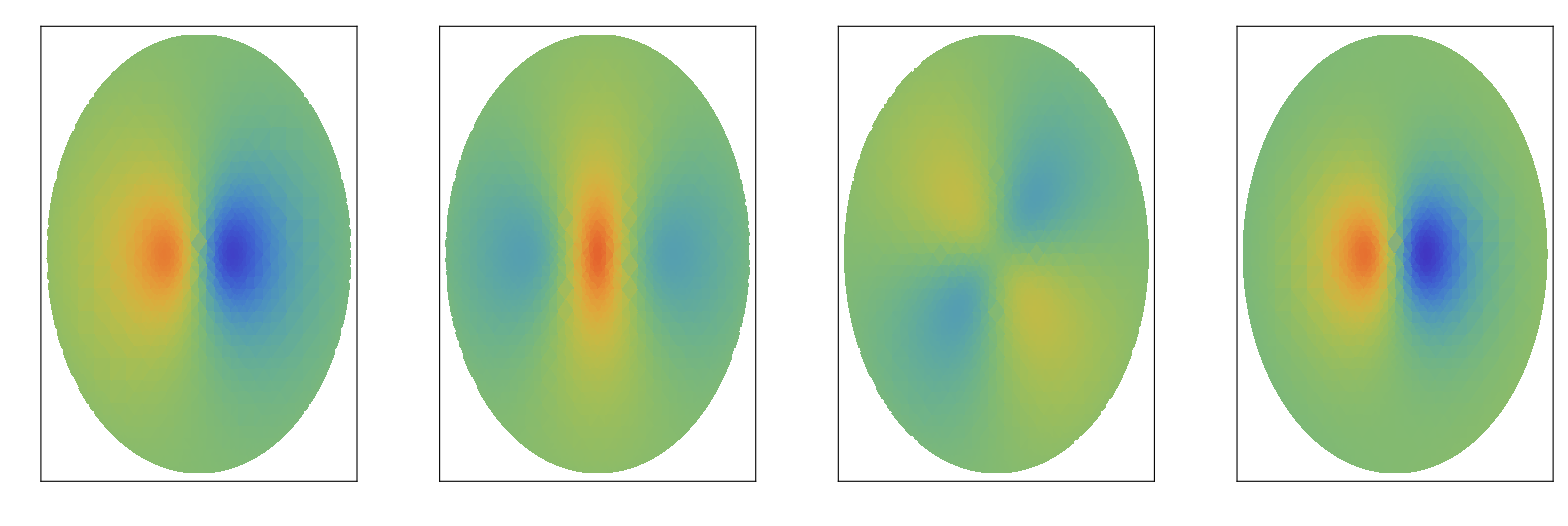

```mathematica
Bs={er.B,B[[1]],B[[2]],B[[3]]}/.{z->Sqrt[rS^2-x^2-y^2],θp->0}//Simplify;
minVal=-0.5;
maxVal=0.5;
p1h=DensityPlot[#,{x,y}∈Disk[{0,0},rS],ColorFunctionScaling->False,ColorFunction->Function[f,ColorData["Rainbow"][(f-minVal)/(maxVal-minVal)]],PlotRange->All,FrameLabel->None,FrameTicks->None,PlotPoints->20]&/@Bs;
bar=BarLegend[{"Rainbow",{minVal,maxVal}}];
GraphicsRow[Insert[ps,bar,-1],AspectRatio->1/4.5,ImageSize->Full]
```

```mathematica
Export["subplots/fig1h.png",p1h];
```